```mathematica
Clear[y];
f[x_,y_]:=y^2-x
```

1

0.1

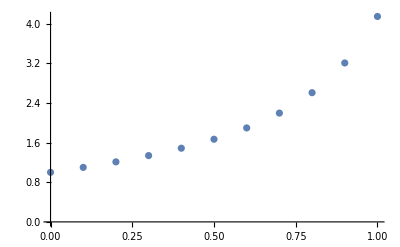

```mathematica
y[0]=1
h=.1
Do[y[n]=y[n-1]+h*f[(n-1)*h,y[n-1]],{n,1,11}]
a=ListPlot[Table[{n*h,y[n]},{n,0,10}]]
```

```mathematica
N[y[11]]
```

5.76208

```mathematica
Clear[y]
```

```mathematica
s=NDSolve[{y'[x]==y[x]^2-x,y[0]==1},y,{x,0,1}]
```

{{y→InterpolatingFunction[…]}}

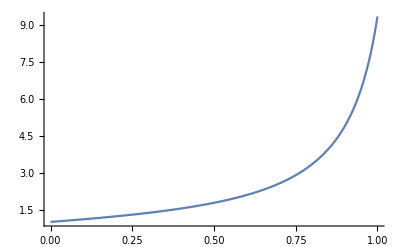

```mathematica
b=Plot[Evaluate[y[x]/.s],{x,0,1},PlotRange->All]
```

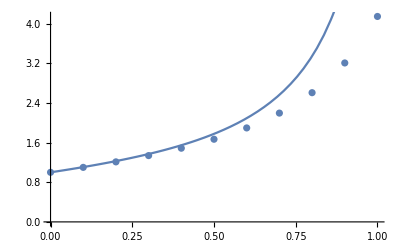

```mathematica
Show[a,b]
```

```mathematica
y[1]/.s
```

{9.35382}

```mathematica
9.353820831189541-3.4951144963411225
```

5.85871

1

0.05

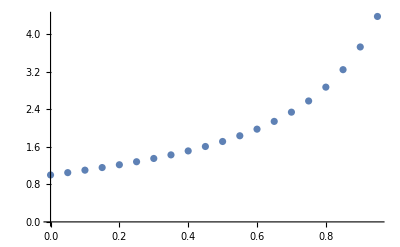

```mathematica
Clear[y]
Clear[a]
f[x_,y_]:=y^2-x
y[0]=1
h=.05
Do[y[n]=y[n-1]+h*f[(n-1)*h,y[n-1]],{n,1,21}]
a=ListPlot[Table[{n*h,y[n]},{n,0,19}]]
```

```mathematica
N[y[21]]
```

6.63897

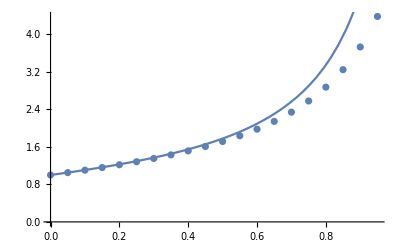

```mathematica
Show[a,b]
```

```mathematica
9.353820831189541-5.778111978411972
```

3.57571